```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

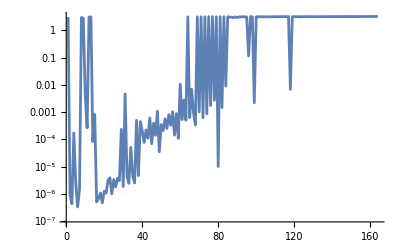

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-19.4325,L2PhaseSet→-37.5213,Q1EkG→133.396,Q2EkG→-155.437,Q3EkG→114.224,Q4EkG→121.878,Q5EkG→-22.16,Q6EkG→-147.312,S1ELkG→778.565,S2ELkG→-4131.75,S3ELkG→-2058.71,S3ERkG→-624.941,S2ERkG→-4538.82,S1ERkG→864.35,PDrive_mean_x→-0.0000803304,PDrive_mean_y→9.07×10^-8,PDrive_sigma_x→0.0000374465,PDrive_sigma_y→0.0000142279,PDrive_xCost→0.0000886296,PDrive_yCost→0.0000142281,PDrive_totalCost→0.0000514289,PDrive_emitSI90_x→0.0001447,PDrive_emitSI90_y→0.0000121121,PDrive_zLen→0.0000122051,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0000804012,PWitness_mean_y→7.599×10^-7,PWitness_sigma_x→0.0000185918,PWitness_sigma_y→0.0000233841,PWitness_xCost→0.0000825228,PWitness_yCost→0.0000233964,PWitness_totalCost→0.0000529596,PWitness_emitSI90_x→0.0000371785,PWitness_emitSI90_y→4.1207×10^-6,PWitness_zLen→6.5877×10^-6,PWitness_zCentroid→991.332,bunchSpacing→0.000145901,transverseCentroidOffset→6.729×10^-7,maximizeMe→3.27731|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -19.4325476092
L2PhaseSet : -37.5212677525
Q1EkG : 133.3959450113
Q2EkG : -155.437210085
Q3EkG : 114.2236340922
Q4EkG : 121.8782579886
Q5EkG : -22.1599987091
Q6EkG : -147.3124043404
S1ELkG : 778.5648122278
S2ELkG : -4131.7473667339
S3ELkG : -2058.7055566081
S3ERkG : -624.9410357792
S2ERkG : -4538.8242740078
S1ERkG : 864.3495989792
PDrive_mean_x : -0.0000803304
PDrive_mean_y : 9.07e-8
PDrive_sigma_x : 0.0000374465
PDrive_sigma_y : 0.0000142279
PDrive_xCost : 0.0000886296
PDrive_yCost : 0.0000142281
PDrive_totalCost : 0.0000514289
PDrive_emitSI90_x : 0.0001446998
PDrive_emitSI90_y : 0.0000121121
PDrive_zLen : 0.0000122051
PDrive_zCentroid : 991.3317037433
PWitness_mean_x : -0.0000804012
PWitness_mean_y : 7.599e-7
PWitness_sigma_x : 0.0000185918
PWitness_sigma_y : 0.0000233841
PWitness_xCost : 0.0000825228
PWitness_yCost : 0.0000233964
PWitness_totalCost : 0.0000529596
PWitness_emitSI90_x : 0.0000371785
PWitness_emitSI90_y : 4.1207e-6
PWitness_zLen : 6.5877e-6
PWitness_zCentroid : 991.3318496444
bunchSpacing : 0.0001459011
transverseCentroidOffset : 6.729e-7
maximizeMe : 3.2773100997

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

6.72935×10^-7

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv